```mathematica
ψ[n_Integer,l_Integer,m_Integer,r_,θ_,ϕ_]:=Module[
{α,Z,Rnl,Ylm},
If[n≤0,Return[0]];
If[l<0,Return[0]];
If[l≥n,Return[0]];
If[Abs[m]>l,Return[0]];
α=0.529177(*Angstrom*);
Z=1.0;

Rnl=√(((2Z)/(n α))^3((n-l-1)!)/((n+l)!*2n))Exp[-(Z r)/(n α)]LaguerreL[n-l-1,2l+1,(2Z r)/(n α)];
If[l≠0,Rnl*=((2Z r)/(n α))^l];
Ylm=SphericalHarmonicY[l,m,θ,ϕ];
Return[Ylm*Rnl]
]

HydrogenOrbitalPlot[n_,l_,m_]:=Module[
{voxels,quads,dτ,rmax,iso},
dτ=75;
rmax=10;
iso=0.005;
voxels=Table[
{
r Sin[θ]Cos[ϕ],
r Sin[θ]Sin[ϕ],
r Cos[θ],
ψ[n,l,m,r,θ,ϕ]//Re
}
,{r,0,rmax,1. rmax/dτ},{θ,0,π,1. π/dτ},{ϕ,-π,π,1.(2π)/dτ}];
quads=Partition[Flatten[voxels],4];
ListContourPlot3D[quads,Contours->iso{-1,1},PlotRange->rmax({{-1, 1}, {-1, 1}, {-1, 1}}),ContourStyle->{Red,Blue}]
]
```

```mathematica
HydrogenOrbitalPlot[2,1,0]
```

-Graphics3D-

```mathematica
ψ[2,0,0,r,θ,ϕ](*/.{r->√(x^2+y^2+z^2),θ->ArcCos[z/(√(x^2+y^2+z^2))],ϕ->ArcTan[y/x]}
Assuming[{x∈Reals,y∈Reals,z∈Reals},Simplify[%]]*)
```

```mathematica
1/(√2)(ψ[2,1,1,r,θ,ϕ]+ψ[2,1,-1,r,θ,ϕ])//Simplify
 -2(0.346204/(√2))Exp[-0.944863r]r Sin[θ]Cos[ϕ]//Simplify
```

-0.244804 ⅇ^(-0.944863 r-ⅈ ϕ) (-1.+1. ⅇ^(2 ⅈ ϕ)) r Sin[θ]

-0.489606 ⅇ^(-0.944863 r) r Cos[ϕ] Sin[θ]

```mathematica
ContourPlot3D[1/(√3)(s2[x,y,z]-px[x,y,z]-py[x,y,z]),{x,-10,10},{y,-10,10},{z,-10,10},Contours->0.05{-1,1},ContourStyle->{Red,Blue},AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

```mathematica
px[x_,y_,z_]:=0.489607Exp[-0.944863 √(x^2+y^2+z^2)]x
py[x_,y_,z_]:=0.489607Exp[-0.944863 √(x^2+y^2+z^2)]y
pz[x_,y_,z_]:=0.489607Exp[-0.944863 √(x^2+y^2+z^2)]zv
s2[x_,y_,z_]:=0.2590887971110992 ⅇ^(-0.9448634388871776 √(x^2+y^2+z^2)) (2.0-1.8897268777743552 √(x^2+y^2+z^2))
pzrot[x_,y_,z_,α_]=α.{px[x,y,z],py[x,y,z],pz[x,y,z]}
```

α.{0.489607 ⅇ^(-0.944863 √(x^2+y^2+z^2)) x,0.489607 ⅇ^(-0.944863 √(x^2+y^2+z^2)) y,0.489607 ⅇ^(-0.944863 √(x^2+y^2+z^2)) z}

{0,0,1}

{0,0,1}

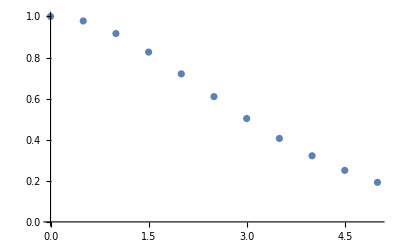

```mathematica
α1=Normalize[{0,0,1}]
α2=Normalize[{0,0,1}]
ts=Table[{t,NIntegrate[pzrot[x-t/2,y,z,α1]pzrot[x+t/2,y,z,α2],{x,-30,30},{y,-30,30},{z,-30,30}]},{t,0.0,5.0,0.5}];

ListPlot[ts]
```